```mathematica
Grid[Partition[Tooltip[Show[ColorConvert[ColorData[#,"Image"],"RGB"],ImageSize->200],#]&/@ColorData["Gradients"],4,4,1,{}],Spacings->.5];
```

```mathematica
ic[x_]:={1/2 1/(2Zeta[3])(x/2)^2/(Exp[x/2]-1),1/8 Boole[1<x<9],1/2 x^2/Exp[x]}[[1]]
```

```mathematica
color="CMYKColors";
```

```mathematica
ColorConvert[ColorData[color,"Image"],"Grayscale"]
```

-Graphics-

```mathematica
SetDirectory["//home/kasper/Documents/KULeuven/PhD/Photon diffusion"];
```

```mathematica
SetDirectory["/localhome/u0131889/Dropbox/Documents/KULeuven/PhD/Photon diffusion"];
```

```mathematica
Monitor[dataraw={};Do[
AppendTo[dataraw, Import[i]]
,{i,FileNames["data/hist*dat"]}],i];
```

```mathematica
Monitor[nraw={};Do[
AppendTo[nraw, Import[i]]
,{i,FileNames["data/occu*dat"]}],i];
```

```mathematica
filename=Import["data/params.txt"]
```

N-1e5.70 dx-0.05 t-100 dt-0.0001 ic-planck c-0.1000 brems

```mathematica
data=dataraw[[-40;;]];
```

```mathematica
data2=Table[{data[[1,i,1]],Mean[data[[;;,i,2]]]},{i,20*20}];
```

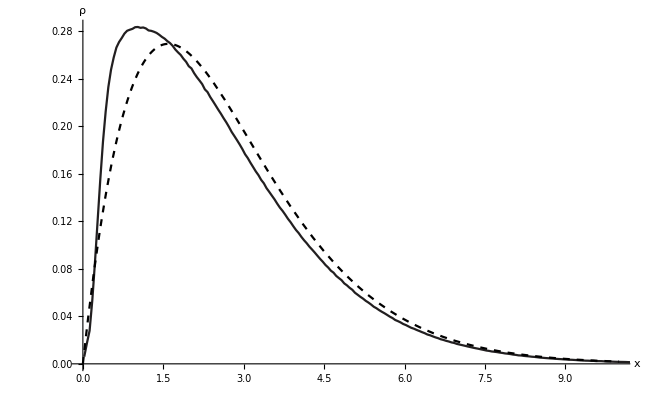

```mathematica
histplot=Show[
ListPlot[data2,PlotRange->{{0,10},All},Joined->True,PlotStyle->Table[ColorData[color,i/(Length[data]-1)],{i,0,Length[data]-1}],(*PlotLegends->BarLegend[{"CMYKColors",{0,2}}],*)Ticks->{Automatic,None},AxesLabel->{"x","ρ"}
],
Plot[{1/(2Zeta[3])x^2/(Exp[x]-1),1/(2Zeta[3]Z[b,k,c])x^2/(Exp[h[x]]-1)},{x,0,10},PlotTheme->"Monochrome",PlotStyle->{Dashed,Dotted},PlotRange->All,Exclusions->None]
]
```

```mathematica
Export["spd "<>filename<>".pdf",histplot];
```

```mathematica
ndata=nraw[[-40;;]];
```

```mathematica
n2=Table[{ndata[[1,i,1]],Mean[ndata[[;;,i,2]]]},{i,20*20}];
```

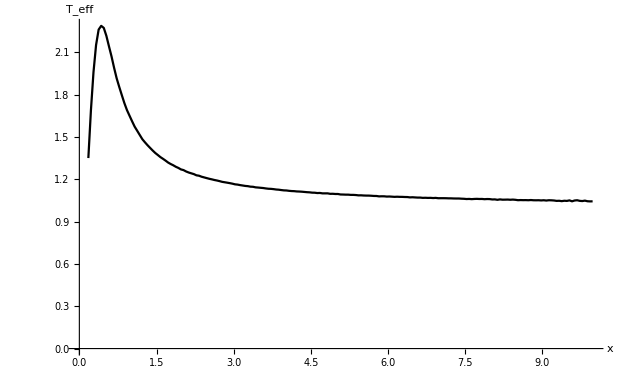

```mathematica
tplot=Show[
ListPlot[Last@TakeList[{#[[1]],#[[1]]/Log[1+1/#[[2]]]}&/@(n2[[1;;10*20]]),{3,All}],PlotRange->{All,All},Joined->{True,False},PlotTheme->"Monochrome",AxesLabel->{"x","T_eff"},PlotMarkers->None]]
```

```mathematica
Export["temp " <> filename <> ".pdf", tplot]
```

temp N-1e5.70 dx-0.05 t-100 dt-0.0001 ic-planck c-0.1000 brems.pdf

```mathematica
c=1/100;b=00/100;k=4/10;
```

```mathematica
x0=1/10;
```

```mathematica
h[x_]:=NIntegrate[Piecewise[{{1,s<=x0},{1+b s^k,s>x0}}]/(1+Piecewise[{{0,s<=x0},{c/s^3,s>x0}}]),{s,0,x}]
```

```mathematica
Clear[Z];Z[b_,k_,c_]:=Z[b,k,c]=Module[{h2},
h2[x_]:=NIntegrate[Piecewise[{{1,s<=x0},{1+b s^k,s>x0}}]/(1+Piecewise[{{0,s<=x0},{c/s^3,s>x0}}]),{s,0,x}];
NIntegrate[1/(2Zeta[3])xx^2/(Exp[h2[xx]]-1),{xx,0,∞}]]
```

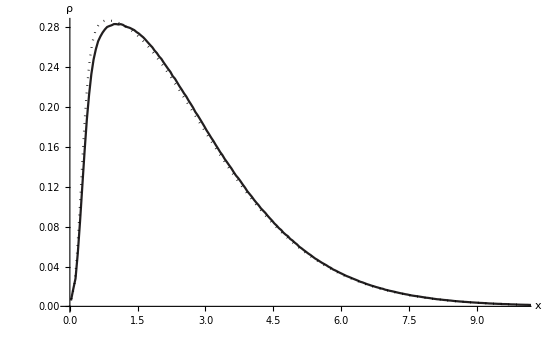

```mathematica
pplot=histplot=Show[
ListPlot[data2,PlotRange->{{0,10},All},Joined->True,PlotStyle->Table[ColorData[color,i/(Length[data]-1)],{i,0,Length[data]-1}],(*PlotLegends->BarLegend[{"CMYKColors",{0,2}}],*)Ticks->{Automatic,None},AxesLabel->{"x","ρ"}
],
Plot[{1/(2Zeta[3]Z[b,k,c])x^2/(Exp[h[x]]-1)},{x,0,10},PlotTheme->"Monochrome",PlotStyle->{Dotted},PlotRange->All,Exclusions->None]
]
```

```mathematica
Export["compare " <>filename<>".pdf",pplot]
```

compare N-1e5.70 dx-0.05 t-100 dt-0.0001 ic-planck c-0.1000 brems.pdf

```mathematica
Z[b,k,c]
```

0.737651

```mathematica
excess=Table[{#[[1]],#[[2]]-1/(2Zeta[3])(#[[1]])^2/(Exp[#[[1]]]-1)}&/@data[[;;]],{i,1,Length[data]}];
```

```mathematica
excessplot=ListPlot[MovingAverage[#,10]&/@excess[[3;;]],Joined->True,PlotStyle->Table[ColorData[color,i/(Length[excess]-1)],{i,0,Length[excess]-1}],
PlotRange->{{0,10},All}(*,PlotLegends->BarLegend[{"CMYKColors",{0,2}}]*)]
```

```mathematica
excessplot=ListPlot[excess[[-1]],Joined->True,PlotStyle->ColorData[color,1],
PlotRange->{{0,1},All}]
```

```mathematica
Export["excess "<>filename<>".pdf", excessplot];
```

```mathematica
ns=Import["data/n.dat"];
```

```mathematica
Length[ns]
```

100001

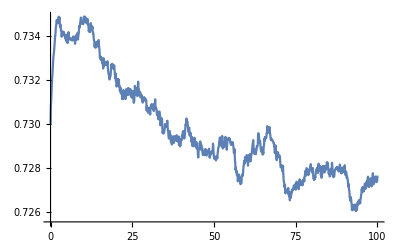

```mathematica
nplot=Show[
ListPlot[ns[[;;;;100]],PlotLegends->Automatic,Joined->True,PlotRange->All],
Plot[{Z[b,k,c]},{x,0,1000},PlotTheme->"Monochrome"]
]
```

```mathematica
hmm ma
```

```mathematica
Export["n "<>filename<>".pdf",nplot];
```